### I1 + I3

#### Work with Andrew

Start

```mathematica
2HeavisideTheta[1-x3](x1^2+(2-x1-x3)^2)/((1-x1)(x1+x3-1))DiracDelta[ρ-(4(1-x1))/(2-x1)^2]HeavisideTheta[x3/(2-x1)-z]HeavisideTheta[2x1+x3-2]HeavisideTheta[2-x1-2x3]
```

Erasing

```mathematica
DiracDelta[ρ-(4(1-x1))/(2-x1)^2]=DiracDelta[ρ-4(1-x1)]=1/4 DiracDelta[]
```

```mathematica
2HeavisideTheta[1-x3] 2/((1-x1)(x1+x3-1))1/4 DiracDelta[x1-(1-ρ/4)]HeavisideTheta[x3-z]HeavisideTheta[2x1+x3-2]
```

#### My work

```mathematica
Integrate[2HeavisideTheta[1-x3] 2/((1-x1)(x1+x3-1))1/4 DiracDelta[x1-(1-ρ/4)]HeavisideTheta[x3-z]HeavisideTheta[2x1+x3-2],{x1,0,1},{x3,0,1}]
```

∫_0^1 -1/(-1+x1)4 DiracDelta[-4+4 x1+ρ] If[2 x1>1&&x1+z>1,UnitStep[1-z] Log[x1/(-1+x1+z)]+UnitStep[1-z,2-2 x1-z] Log[-1-z/(-1+x1)],Integrate[UnitStep[1-x3,-2+2 x1+x3,x3-z]/(-1+x1+x3),{x3,0,1},Assumptions→(0<Re[x1]&&Im[x1]==0)&&(((Re[x1]<1&&Im[x1]==0)&&(Re[z]<1&&Im[z]==0)&&x1+z≤1)||2 x1≤1)]]ⅆx1

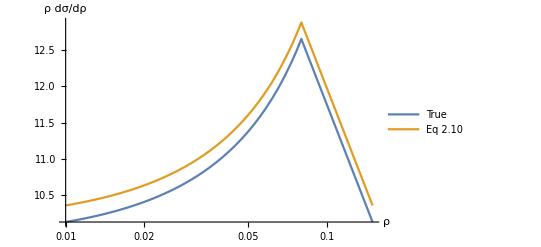

```mathematica
zval=0.04;
LogLinearPlot[{
(*ρ(HeavisideTheta[ρ-(2z-z^2)]((-12(6-6 √(1-ρ)+ρ(5 √(1-ρ)-8+2ρ)))/(ρ^3(1-ρ))-(2(6-6 √(1-ρ)-ρ(5-4 √(1-ρ))))/(ρ^2(1-ρ))Log[ρ/(2+2 √(1-ρ)-3ρ)])
+HeavisideTheta[2z-z^2-ρ]((12(1-2z)(2-2 √(1-ρ)-ρ)^2)/(ρ^3(2-2 √(1-ρ)-ρ(2-√(1-ρ))))-(2(6-6 √(1-ρ)-ρ(5-4 √(1-ρ))))/(ρ^2(1-ρ))Log[(2-4z(1-z-√(1-ρ))-2 √(1-ρ)-ρ)/(4z(1-z)-ρ)]))/.{z->zval},*)
(HeavisideTheta[ρ-2z](-3-4Log[ρ/2]+4Log[2])
+HeavisideTheta[2z-ρ](-3-4Log[z]-4Log[1-ρ/(4z)]))/.{z->zval},
(HeavisideTheta[ρ-2z](-4Log[(2 ρ)/4])
+HeavisideTheta[2z-ρ](-4 Log[(2 (-4 z+ρ))/-4]))/.{z->zval}(*,
(HeavisideTheta[ρ-2z]ρ(3-4/ρ-4 ArcTanh[1-ρ/2]+Log[4]-(8 Log[-(2 ρ)/(-4+ρ)])/ρ)/2
+HeavisideTheta[2z-ρ](-4+8 z-ρ+ρ Log[4]+2 ρ Log[(-4 z+ρ)/(-4+ρ)]-8 Log[(2 (-4 z+ρ))/(-4+ρ)])/2)/.{z->zval}*)},
{ρ,0.01,0.15},PlotLegends->{"True","Eq 2.10","Lowest-order approx, \nλ all the way through", "λ dropped before final integration"},AxesLabel->{"ρ","ρ dσ/dρ"}]
```

```mathematica
Series[((x1^2+(2-x1-x3)^2)/((1-x1)(x1+x3-1))1/(4λ)/.{x1->1-λ(1-x1),x3->λ x3})/.{x1->1-ρ/4},{λ,0,1}]
```

2/((x3-ρ/4) ρ λ^3)-(2 x3)/(((x3-ρ/4) ρ) λ^2)+(8 x3^2-4 x3 ρ+ρ^2)/(8 (x3-ρ/4) ρ λ)+O[λ]^2

```mathematica
FullSimplify[2/((x3-ρ/4) ρ λ^3)-(2 x3)/(((x3-ρ/4) ρ) λ^2)]
```

(8-8 x3 λ)/(λ^3 (4 x3-ρ) ρ)

```mathematica
Series[(8-8 x3 λ)/(λ^3 (4 x3-ρ) ρ),{λ,0,1}]
```

8/((4 x3-ρ) ρ λ^3)-(8 x3)/(((4 x3-ρ) ρ) λ^2)+O[λ]^2

```mathematica
FullSimplify[Assuming[{0<λ<1,0<z<1,0<ρ<1},Integrate[8/((4 x3-ρ) ρ λ^3)-(8 x3)/(((4 x3-ρ) ρ) λ^2),{x3,ρ/(2λ),(4+ρ)/(8λ)}]]/.λ->1]
```

(-4+ρ (3+Log[4])-8 Log[-(2 ρ)/(-4+ρ)]+2 ρ Log[-ρ/(-4+ρ)])/(4 ρ)

```mathematica
FullSimplify[(2(1-x3))/(4(1-x1)(x1+x3-1))/.{x1->1-ρ/4}]
```

(8-8 x3)/(4 x3 ρ-ρ^2)

```mathematica
i1Part1=Assuming[0<ρ<1,Integrate[(8(1-x3))/(ρ(4x3-ρ)),{x3,ρ/2,(4+ρ)/8}]]
i1Part2=Assuming[{0<z<1,0<ρ<2z,8z≠4+ρ},Integrate[(8(1-x3))/(ρ(4x3-ρ)),{x3,z,(4+ρ)/8}]]
```

(-4+3 ρ-4 ρ ArcTanh[1-ρ/2]+ρ Log[4]-8 Log[-(2 ρ)/(-4+ρ)])/(4 ρ)

(-4+8 z-ρ+ρ Log[4]+2 ρ Log[(-4 z+ρ)/(-4+ρ)]-8 Log[(2 (-4 z+ρ))/(-4+ρ)])/(4 ρ)

```mathematica
FullSimplify[i1Part1]
```

-4 ArcTanh[1-ρ/2]+(-4+ρ (3+Log[4])-8 Log[-(2 ρ)/(-4+ρ)])/ρ

```mathematica
FullSimplify[i1Part2]
```

(-4+8 z+ρ (-1+Log[4])+2 ρ Log[(-4 z+ρ)/(-4+ρ)]-8 Log[(2 (-4 z+ρ))/(-4+ρ)])/ρ

### I3

```mathematica
Series[(4(x1+x3-1))/(x1+x3)^2/.{x1->1-λ(1-x1),x3->λ x3},{λ,0,1}]
```

4 (-1+x1+x3) λ+O[λ]^2